```mathematica
Timing[Prime[10000000000]]
```

{0.690493,252097800623}

```mathematica
g=CompleteGraph[6]
```

-Graphics-

```mathematica
Needs["GraphUtilities`"];
```

```mathematica
HamiltonianCycles[CompleteGraph[6],All]
```

{{1,2,3,4,5,6},{1,2,3,4,6,5},{1,2,3,5,4,6},{1,2,3,5,6,4},{1,2,3,6,4,5},{1,2,3,6,5,4},{1,2,4,3,5,6},{1,2,4,3,6,5},{1,2,4,5,3,6},{1,2,4,5,6,3},{1,2,4,6,3,5},{1,2,4,6,5,3},{1,2,5,3,4,6},{1,2,5,3,6,4},{1,2,5,4,3,6},{1,2,5,4,6,3},{1,2,5,6,3,4},{1,2,5,6,4,3},{1,2,6,3,4,5},{1,2,6,3,5,4},{1,2,6,4,3,5},{1,2,6,4,5,3},{1,2,6,5,3,4},{1,2,6,5,4,3},{1,3,2,4,5,6},{1,3,2,4,6,5},{1,3,2,5,4,6},{1,3,2,5,6,4},{1,3,2,6,4,5},{1,3,2,6,5,4},{1,3,4,2,5,6},{1,3,4,2,6,5},{1,3,4,5,2,6},{1,3,4,5,6,2},{1,3,4,6,2,5},{1,3,4,6,5,2},{1,3,5,2,4,6},{1,3,5,2,6,4},{1,3,5,4,2,6},{1,3,5,4,6,2},{1,3,5,6,2,4},{1,3,5,6,4,2},{1,3,6,2,4,5},{1,3,6,2,5,4},{1,3,6,4,2,5},{1,3,6,4,5,2},{1,3,6,5,2,4},{1,3,6,5,4,2},{1,4,2,3,5,6},{1,4,2,3,6,5},{1,4,2,5,3,6},{1,4,2,5,6,3},{1,4,2,6,3,5},{1,4,2,6,5,3},{1,4,3,2,5,6},{1,4,3,2,6,5},{1,4,3,5,2,6},{1,4,3,5,6,2},{1,4,3,6,2,5},{1,4,3,6,5,2},{1,4,5,2,3,6},{1,4,5,2,6,3},{1,4,5,3,2,6},{1,4,5,3,6,2},{1,4,5,6,2,3},{1,4,5,6,3,2},{1,4,6,2,3,5},{1,4,6,2,5,3},{1,4,6,3,2,5},{1,4,6,3,5,2},{1,4,6,5,2,3},{1,4,6,5,3,2},{1,5,2,3,4,6},{1,5,2,3,6,4},{1,5,2,4,3,6},{1,5,2,4,6,3},{1,5,2,6,3,4},{1,5,2,6,4,3},{1,5,3,2,4,6},{1,5,3,2,6,4},{1,5,3,4,2,6},{1,5,3,4,6,2},{1,5,3,6,2,4},{1,5,3,6,4,2},{1,5,4,2,3,6},{1,5,4,2,6,3},{1,5,4,3,2,6},{1,5,4,3,6,2},{1,5,4,6,2,3},{1,5,4,6,3,2},{1,5,6,2,3,4},{1,5,6,2,4,3},{1,5,6,3,2,4},{1,5,6,3,4,2},{1,5,6,4,2,3},{1,5,6,4,3,2},{1,6,2,3,4,5},{1,6,2,3,5,4},{1,6,2,4,3,5},{1,6,2,4,5,3},{1,6,2,5,3,4},{1,6,2,5,4,3},{1,6,3,2,4,5},{1,6,3,2,5,4},{1,6,3,4,2,5},{1,6,3,4,5,2},{1,6,3,5,2,4},{1,6,3,5,4,2},{1,6,4,2,3,5},{1,6,4,2,5,3},{1,6,4,3,2,5},{1,6,4,3,5,2},{1,6,4,5,2,3},{1,6,4,5,3,2},{1,6,5,2,3,4},{1,6,5,2,4,3},{1,6,5,3,2,4},{1,6,5,3,4,2},{1,6,5,4,2,3},{1,6,5,4,3,2}}

```mathematica
Length[Out[5]]
```

120

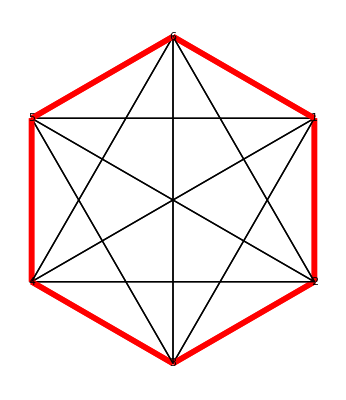
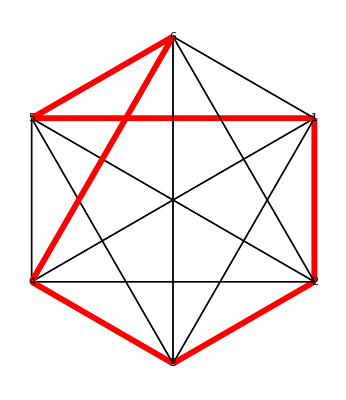
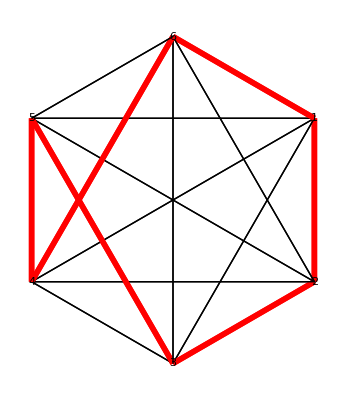
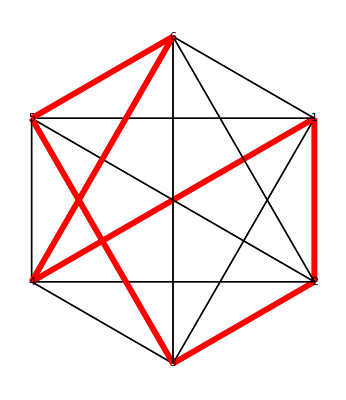
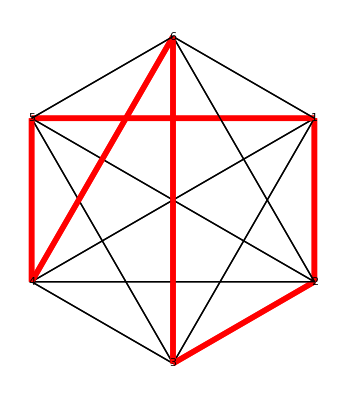
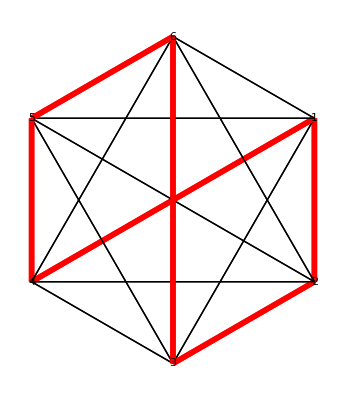
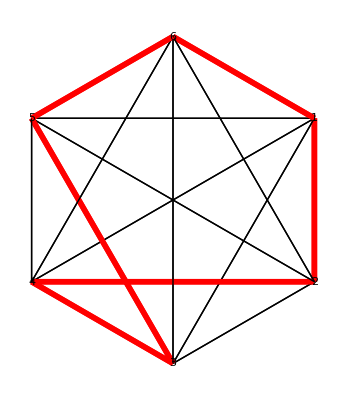
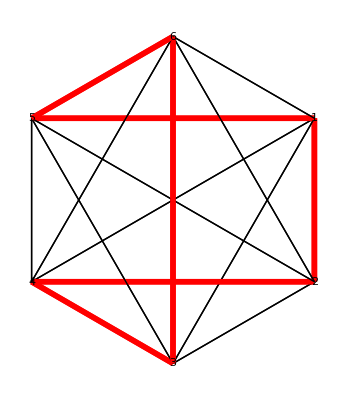
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Block[{cs=Transpose[{Out[5][[i]],RotateRight[Out[5][[i]]]}]},GraphPlot[g,EdgeRenderingFunction->(If[MemberQ[cs,#2]||MemberQ[cs,Reverse[#2]],{Red,Thickness[.01],Line[#1]},{Black,Line[#1]}]&),VertexLabeling->True]],{i,1,120}]
```

{{1,2},{3,4},{5,6}}

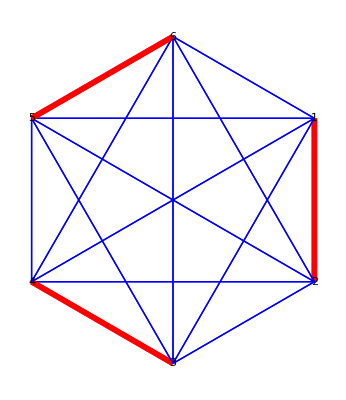

```mathematica
match=MaximalIndependentEdgeSet[g]
GraphPlot[g,EdgeRenderingFunction->({If[MemberQ[match,#2]||MemberQ[match,Reverse[#2]],{Red,Thickness[0.01],Line[#]},{Blue,Line[#]}]}&),VertexLabeling->True]
```

{1}

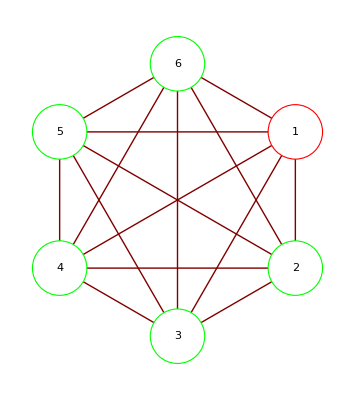

```mathematica
m=MaximalIndependentVertexSet[g]
GraphPlot[g,VertexRenderingFunction->({EdgeForm[If[MemberQ[m,#2],Red,Green]],White,Disk[#1,.2],Black,Text[#2,#1]}&)]
```

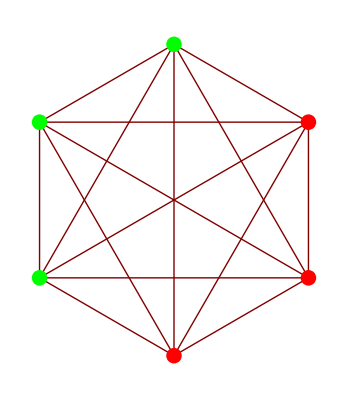

```mathematica
Block[{c=MinCut[g,2]},
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[c⟦1⟧,#2],Red,Green],Disk[#1,.05]}&)]]
```

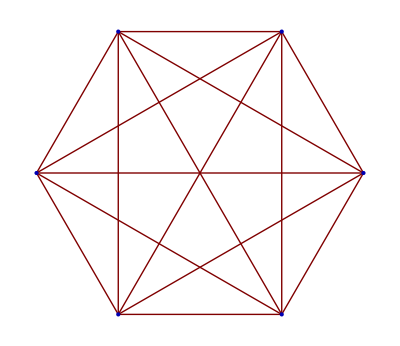
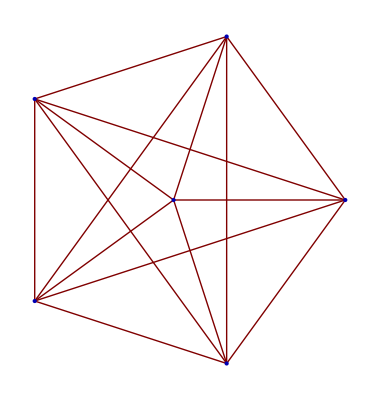
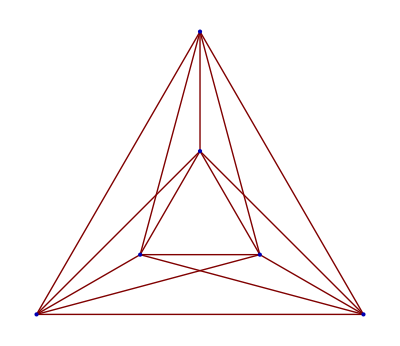

```mathematica
GraphData[{"Complete",6},"AllImages"]
```

```mathematica
GraphData[{"Complete",6},"ChromaticPolynomial"][x]//TraditionalForm
```

(x-5) (x-4) (x-3) (x-2) (x-1) x

```mathematica
Table[{i,GraphData[{"Complete",6},i]},{i,{"ArcTransitivity","ArticulationVertices","AutomorphismCount","Automorphisms","Bridges","CliqueNumber","Corank","CrossingNumber","Degrees","DeterminedByResistance","DeterminedBySpectrum","DetourMatrix","Diameter","Eccentricities","Genus","Girth","HamiltonianCycleCount","HamiltonianCycles","HamiltonianPathCount","HamiltonianPaths","IndependenceNumber","LovaszNumber","Rank","RectilinearCrossingNumber","ResistanceMatrix","ShannonCapacity","SpanningTreeCount","Spectrum","ToroidalCrossingNumber","Unitransitivity","BalabanIndex","CyclomaticNumber","DetourIndex","HararyIndex","HosoyaIndex","KirchhoffIndex","KirchhoffSumIndex","MolecularTopologicalIndex","StabilityIndex","TopologicalIndex","WeinerIndex","WeinerSumIndex","ZIndex","ChromaticallyUnique","ChromaticInvariant","ChromaticNumber","EdgeChromaticNumber","ComplementGraph","DualGraph","Graph","LineGraph","ComplementGraph","DualGraph","Graph","LineGraph","AllImages","AllVertexCoordinates","Image","Image3D","LabeledImage","VertexCoordinates","Connected","ConnectedComponentCount","ConnectedComponentGraphNames","ConnectedComponentIndices","Disconnected","EdgeConnectivity","Triangulated","VertexConnectivity"}}]//Column
```

GraphData::notprop: "\"WeinerIndex\"" is not a known property for GraphData. Use GraphData["Properties"] for a list of properties.

GraphData::notprop: "\"WeinerSumIndex\"" is not a known property for GraphData. Use GraphData["Properties"] for a list of properties.

{ArcTransitivity,2}
{ArticulationVertices,{}}
{AutomorphismCount,720}
{Automorphisms,Missing[TooLarge]}
{Bridges,{}}
{CliqueNumber,6}
{Corank,10}
{CrossingNumber,3}
{Degrees,{5,5,5,5,5,5}}
{DeterminedByResistance,True}
{DeterminedBySpectrum,True}
{DetourMatrix,{{0,5,5,5,5,5},{5,0,5,5,5,5},{5,5,0,5,5,5},{5,5,5,0,5,5},{5,5,5,5,0,5},{5,5,5,5,5,0}}}
{Diameter,1}
{Eccentricities,{1,1,1,1,1,1}}
{Genus,1}
{Girth,3}
{HamiltonianCycleCount,120}
{HamiltonianCycles,{{1,2,3,4,5,6},{1,2,3,4,6,5},{1,2,3,5,4,6},{1,2,3,5,6,4},{1,2,3,6,4,5},{1,2,3,6,5,4},{1,2,4,3,5,6},{1,2,4,3,6,5},{1,2,4,5,3,6},{1,2,4,5,6,3},{1,2,4,6,3,5},{1,2,4,6,5,3},{1,2,5,3,4,6},{1,2,5,3,6,4},{1,2,5,4,3,6},{1,2,5,4,6,3},{1,2,5,6,3,4},{1,2,5,6,4,3},{1,2,6,3,4,5},{1,2,6,3,5,4},{1,2,6,4,3,5},{1,2,6,4,5,3},{1,2,6,5,3,4},{1,2,6,5,4,3},{1,3,2,4,5,6},{1,3,2,4,6,5},{1,3,2,5,4,6},{1,3,2,5,6,4},{1,3,2,6,4,5},{1,3,2,6,5,4},{1,3,4,2,5,6},{1,3,4,2,6,5},{1,3,4,5,2,6},{1,3,4,5,6,2},{1,3,4,6,2,5},{1,3,4,6,5,2},{1,3,5,2,4,6},{1,3,5,2,6,4},{1,3,5,4,2,6},{1,3,5,4,6,2},{1,3,5,6,2,4},{1,3,5,6,4,2},{1,3,6,2,4,5},{1,3,6,2,5,4},{1,3,6,4,2,5},{1,3,6,4,5,2},{1,3,6,5,2,4},{1,3,6,5,4,2},{1,4,2,3,5,6},{1,4,2,3,6,5},{1,4,2,5,3,6},{1,4,2,5,6,3},{1,4,2,6,3,5},{1,4,2,6,5,3},{1,4,3,2,5,6},{1,4,3,2,6,5},{1,4,3,5,2,6},{1,4,3,5,6,2},{1,4,3,6,2,5},{1,4,3,6,5,2},{1,4,5,2,3,6},{1,4,5,2,6,3},{1,4,5,3,2,6},{1,4,5,3,6,2},{1,4,5,6,2,3},{1,4,5,6,3,2},{1,4,6,2,3,5},{1,4,6,2,5,3},{1,4,6,3,2,5},{1,4,6,3,5,2},{1,4,6,5,2,3},{1,4,6,5,3,2},{1,5,2,3,4,6},{1,5,2,3,6,4},{1,5,2,4,3,6},{1,5,2,4,6,3},{1,5,2,6,3,4},{1,5,2,6,4,3},{1,5,3,2,4,6},{1,5,3,2,6,4},{1,5,3,4,2,6},{1,5,3,4,6,2},{1,5,3,6,2,4},{1,5,3,6,4,2},{1,5,4,2,3,6},{1,5,4,2,6,3},{1,5,4,3,2,6},{1,5,4,3,6,2},{1,5,4,6,2,3},{1,5,4,6,3,2},{1,5,6,2,3,4},{1,5,6,2,4,3},{1,5,6,3,2,4},{1,5,6,3,4,2},{1,5,6,4,2,3},{1,5,6,4,3,2},{1,6,2,3,4,5},{1,6,2,3,5,4},{1,6,2,4,3,5},{1,6,2,4,5,3},{1,6,2,5,3,4},{1,6,2,5,4,3},{1,6,3,2,4,5},{1,6,3,2,5,4},{1,6,3,4,2,5},{1,6,3,4,5,2},{1,6,3,5,2,4},{1,6,3,5,4,2},{1,6,4,2,3,5},{1,6,4,2,5,3},{1,6,4,3,2,5},{1,6,4,3,5,2},{1,6,4,5,2,3},{1,6,4,5,3,2},{1,6,5,2,3,4},{1,6,5,2,4,3},{1,6,5,3,2,4},{1,6,5,3,4,2},{1,6,5,4,2,3},{1,6,5,4,3,2}}}
{HamiltonianPathCount,720}
{HamiltonianPaths,Missing[TooLarge]}
{IndependenceNumber,1}
{LovaszNumber,1}
{Rank,5}
{RectilinearCrossingNumber,3}
{ResistanceMatrix,SparseArray[<30>,{6,6}]}
{ShannonCapacity,1}
{SpanningTreeCount,1296}
{Spectrum,{-1,-1,-1,-1,-1,5}}
{ToroidalCrossingNumber,0}
{Unitransitivity,2}
{BalabanIndex,45/11}
{CyclomaticNumber,10}
{DetourIndex,75}
{HararyIndex,30}
{HosoyaIndex,76}
{KirchhoffIndex,5}
{KirchhoffSumIndex,5}
{MolecularTopologicalIndex,300}
{StabilityIndex,66}
{TopologicalIndex,-320}
{WeinerIndex,GraphData[{Complete,6},WeinerIndex]}
{WeinerSumIndex,GraphData[{Complete,6},WeinerSumIndex]}
{ZIndex,76}
{ChromaticallyUnique,True}
{ChromaticInvariant,24}
{ChromaticNumber,6}
{EdgeChromaticNumber,5}
{ComplementGraph,-Graphics-}
{DualGraph,-Graphics-}
{Graph,-Graphics-}
{LineGraph,-Graphics-}
{ComplementGraph,-Graphics-}
{DualGraph,-Graphics-}
{Graph,-Graphics-}
{LineGraph,-Graphics-}
{AllImages,{-Graphics-,-Graphics-,-Graphics-}}
{AllVertexCoordinates,{{{-0.5,-0.866},{0.5,-0.866},{1.,0.},{0.5,0.866},{-0.5,0.866},{-1.,0.}},{{1.,0.},{0.309,0.9511},{-0.809,0.5878},{-0.809,-0.5878},{0.309,-0.9511},{0.,0.}},{{1.2167,-0.88935},{1.4709,-0.74255},{1.6177,-0.48815},{1.6177,-0.19445},{1.7644,-0.74255},{2.0186,-0.88935}}}}
{Image,-Graphics-}
{Image3D,-Graphics3D-}
{LabeledImage,-Graphics-}
{VertexCoordinates,{{-0.5,-0.866},{0.5,-0.866},{1.,0.},{0.5,0.866},{-0.5,0.866},{-1.,0.}}}
{Connected,True}
{ConnectedComponentCount,1}
{ConnectedComponentGraphNames,{{Complete,6}}}
{ConnectedComponentIndices,{{1,2,3,4,5,6}}}
{Disconnected,False}
{EdgeConnectivity,5}
{Triangulated,False}
{VertexConnectivity,5}

```mathematica
Join[{"ArcTransitivity","ArticulationVertices","AutomorphismCount","Automorphisms","Bridges","CliqueNumber","Corank","CrossingNumber","Degrees","DeterminedByResistance","DeterminedBySpectrum","DetourMatrix","Diameter","Eccentricities","Genus","Girth","HamiltonianCycleCount","HamiltonianCycles","HamiltonianPathCount","HamiltonianPaths","IndependenceNumber","LovaszNumber","Rank","RectilinearCrossingNumber","ResistanceMatrix","ShannonCapacity","SpanningTreeCount","Spectrum","ToroidalCrossingNumber","Unitransitivity"},
{"BalabanIndex","CyclomaticNumber","DetourIndex","HararyIndex","HosoyaIndex","KirchhoffIndex","KirchhoffSumIndex","MolecularTopologicalIndex","StabilityIndex","TopologicalIndex","WeinerIndex","WeinerSumIndex","ZIndex"},
{"ChromaticallyUnique","ChromaticInvariant","ChromaticNumber","EdgeChromaticNumber"},
{"ComplementGraph","DualGraph","Graph","LineGraph"},
{"ComplementGraph","DualGraph","Graph","LineGraph"},
{"AllImages","AllVertexCoordinates","Image","Image3D","LabeledImage","VertexCoordinates"},
{"Connected","ConnectedComponentCount","ConnectedComponentGraphNames","ConnectedComponentIndices","Disconnected","EdgeConnectivity","Triangulated","VertexConnectivity"}]
```

```mathematica
GraphPlot3D[CompleteGraph[24]];
```

```mathematica
strm=OpenWrite["output.log"];
```

```mathematica
Monitor[Do[Block[{mat=Partition[Permute[Range[16],RandomPermutation[16]],4]},Piecewise[{{mat>>>"output.log",Abs[Det[mat]]<2},{0,Abs[Det[mat]]>1}}]],{i,100000}],i]
```

```mathematica
Det[{{4,2,1,13},{12,7,14,6},{10,9,8,16},{5,15,3,11}}]
```

0

```mathematica
f[x_,logname_,range_]:=Monitor[Do[Block[{mat=Partition[Permute[Range[x^2],RandomPermutation[x^2]],x]},Piecewise[{{mat>>>StringJoin[logname,".log"],Abs[Det[mat]]<2},{0,Abs[Det[mat]]>1}}]],{i,range}],i]
```

```mathematica
matmlogran[x_,logname_,range_]:=Monitor[Do[Block[{mat=Partition[Permute[Range[x^2],RandomPermutation[x^2]],x]},
Block[{d=Abs[Det[mat]]},
Piecewise[{{mat>>>StringJoin[logname,".log"],d<2},{0,d>1}}]
]
],{i,range}],i]
```

```mathematica
cFun2=Compile[{{x,_Integer},{logname,_Integer},{range,_Integer}},Monitor[Do[Block[{mat=Partition[Permute[Range[x^2],RandomPermutation[x^2]],x]},
Block[{d=Abs[Det[mat]]},
Piecewise[{{mat>>>StringJoin[logname,".log"],d<2},{0,d>1}}]
]
],{i,range}],i];1,CompilationTarget->"C"]
```

CompiledFunction[{x,logname,range},Monitor[Do[Block[{mat=Partition[Permute[Range[x^2],RandomPermutation[x^2]],x]},Block[{d=Abs[Det[mat]]},Piecewise[{{mat>>>logname<>.log, d<2}, {0, d>1}}]]],{i,range}],i];1,-CompiledCode-]

```mathematica
<<CCodeGenerator`
```

```mathematica
Null;1
```

1

```mathematica
cFun=Compile[{{x,_Integer},{logname,_Integer},{range,_Integer}},Monitor[Do[Block[{mat=Partition[Permute[Range[x^2],RandomPermutation[SymmetricGroup[x^2]]],x]},Piecewise[{{mat>>>StringJoin["output",ToString[logname],".log"],Abs[Det[mat]]<2},{0,Abs[Det[mat]]>1}}]],{i,range}],i];1,CompilationTarget->"C"]
```

CompiledFunction[{x,logname,range},Monitor[Do[Block[{mat=Partition[Permute[Range[x^2],RandomPermutation[SymmetricGroup[x^2]]],x]},Piecewise[{{mat>>>output<>ToString[logname]<>.log, Abs[Det[mat]]<2}, {0, Abs[Det[mat]]>1}}]],{i,range}],i];1,-CompiledCode-]

```mathematica
Table[{Timing[cFun2[6,0,10^n]],Timing[f2[6,"output",10^n]]},{n,1,6}]//Column
```

```mathematica
Timing[cFun2[6,0,1000]]
Timing[f2[6,"output",1000]]
```

{0.122243,1}

{0.12574,Null}

```mathematica
Timing[cFun2[6,0,10000]]
Timing[f2[6,"output",10000]]
```

{1.18164,1}

{1.17474,Null}

```mathematica
Timing[cFun2[6,0,100000]]
Timing[f2[6,"output",100000]]
```

{11.7605,1}

{11.6629,Null}

```mathematica
Timing[cFun2[6,0,1000000]]
Timing[f2[6,"output",1000000]]
```

{118.564,1}

{115.851,Null}

```mathematica
2435.65/115.851
```

21.024

```mathematica
Timing[cFun2[5,0,1000000]]
Timing[f2[5,"output",1000000]]
```

StringJoin::string: String expected at position 1 in 0 <> ".log".

General::stream: 0 <> ".log" is not a string, InputStream[ ], or OutputStream[ ].

General::stop: Further output of General :: stream will be suppressed during this calculation.

{106.704,1}

{108.079,Null}

```mathematica
Timing[cFun2[5,0,100000]]
Timing[f2[5,"output",100000]]
```

{10.4282,1}

{10.4097,Null}

```mathematica
Timing[cFun[5,0,100000]]
Timing[f[5,"output",100000]]
```

{17.1011,1}

{16.3723,Null}

```mathematica
Timing[cFun[4,0,100000]]
```

{8.01484,1}

```mathematica
Timing[f[4,"output",100000]]
```

{7.36933,Null}

```mathematica
CCodeStringGenerate[cFun,"compute"]
```

CCodeGenerate::wmreq: The expression Function[{x, logname, range}, Monitor[Do[Block[{mat = Partition[Permute[Range[« 1 »], RandomPermutation[« 1 »]], x]}, TagBox[GridBox[{{"{", GridBox[{{mat >>> StringJoin[« 3 »], Abs[« 1 »] < 2}, {"0", Abs[« 1 »] > 1}}, ColumnAlignments -> {Left}, ColumnSpacings -> 1.2, ColumnWidths -> Automatic, AllowedDimensions -> {2, Automatic}, Selectable -> True, Editable -> True]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 0.5, ColumnWidths -> Automatic], "Piecewise", Rule[SyntaxForm, Equal], Rule[SelectWithContents, True], Rule[Selectable, False], Rule[Editable, False], Rule[DeleteWithContents, True]]], {i, range}], i]] requires Mathematica to be evaluated.   The function will be generated but can be expected to fail with a nonzero error code when executed.

#include "math.h"

#include "WolframRTL.h"

static WolframCompileLibrary_Functions funStructCompile;

static void * E0 = 0;


static mbool initialize = 1;

#include "compute.h"

DLLEXPORT int Initialize_compute(WolframLibraryData libData)
{
if( initialize)
{
funStructCompile = libData->compileLibraryFunctions;
{
E0 = funStructCompile->getExpressionFunctionPointer(libData, "Hold[Function[List[x, logname, range], Monitor[Do[Block[List[Set[mat, Partition[Permute[Range[Power[x, 2]], RandomPermutation[SymmetricGroup[Power[x, 2]]]], x]]], Piecewise[List[List[PutAppend[mat, StringJoin[\"output\", ToString[logname], \".log\"]], Less[Abs[Det[mat]], 2]], List[0, Greater[Abs[Det[mat]], 1]]]]], List[i, range]], i]]]");
}
if( E0 == 0)
{
return LIBRARY_FUNCTION_ERROR;
}
initialize = 0;
}
return 0;
}

DLLEXPORT void Uninitialize_compute(WolframLibraryData libData)
{
if( !initialize)
{
initialize = 1;
}
}

DLLEXPORT int compute(WolframLibraryData libData, mint A1, mint A2, mint A3, mreal *Res)
{
mint I0_0;
mint I0_1;
mint I0_2;
mreal R0_0;
int err = 0;
I0_0 = A1;
I0_1 = A2;
I0_2 = A3;
{
int S0[3];
void * S1[3];
S0[0] = 2;
S1[0] = (void*) (&I0_0);
S0[1] = 2;
S1[1] = (void*) (&I0_1);
S0[2] = 2;
S1[2] = (void*) (&I0_2);
err = funStructCompile->evaluateFunctionExpression(libData, E0, 0, 0, 3, S0, S1, 3, 0, (void*) (&R0_0));
if( err)
{
goto error_label;
}
}
*Res = R0_0;
error_label:
funStructCompile->WolframLibraryData_cleanUp(libData, 1);
return err;
}

```mathematica
Interpolation[{{3,286/100},{4,2662/100},{5,27971/100}}]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

InterpolatingFunction[{{3,5}},<>]

```mathematica
Plot[%[i],{i,3,10}]
```

-Graphics-

```mathematica
N[Log[5000000]/Log[10]]
```

6.69897